```mathematica
ListPlot[{0,661.6},{20π/180,609.766},{40π/180,504.285},{60π/180,398.209},{80π/180,313.879},{100π/180,256.492},{120π/180,215.232}]
```

ListPlot::nonopt: ListPlot[{0,661.6},{π/9,609.766},{(2 π)/9,504.285},{π/3,398.209},{(4 π)/9,313.879},{(5 π)/9,256.492},{(2 π)/3,215.232}] 中位置 1 外应该是选项（而不是 {(2 π)/3,215.232}）. 选项必须是一个规则或者规则列表.

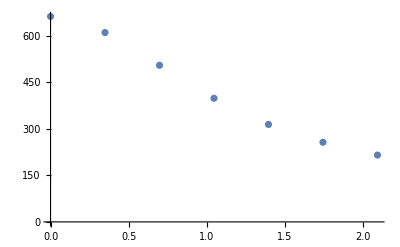

```mathematica
ListPlot[{{0,661.6},{π/9,609.766},{(2 π)/9,504.285},{π/3,398.209},{(4 π)/9,313.879},{(5 π)/9,256.492},{(2 π)/3,215.232}}]
```

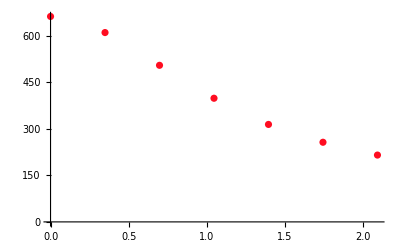

```mathematica
ListPlot[{{0,661.6},{π/9,609.766},{(2 π)/9,504.285},{π/3,398.209},{(4 π)/9,313.879},{(5 π)/9,256.492},{(2 π)/3,215.232}},PlotStyle->RGBColor[1.,0.05,0.13]]
```

```mathematica
Table[661.6/(1+661.6/511 *(1-Cos[x*20π/180])),{x,0,6}]
```

```mathematica
X={661.6,613.6830486036567,507.78795228420825,401.61273461629844,319.63033780907716,262.58747358539773,224.87534920846082}
```

{661.6,613.683,507.788,401.613,319.63,262.587,224.875}

```mathematica
Y={661.6,609.766,504.285,398.209,313.879,256.492,215.232}
```

{661.6,609.766,504.285,398.209,313.879,256.492,215.232}

```mathematica
(X-Y)/X *100
```

{0.,0.638285,0.689845,0.847517,1.79937,2.32131,4.28831}

```mathematica
Y=Y/1000
```

{0.6616,0.609766,0.504285,0.398209,0.313879,0.256492,0.215232}

```mathematica
R=1.125238-0.19095*Y-8.55161*Y^2+21.15405*Y^3-20.20699*Y^4+6.96786*Y^5
```

{0.393481,0.419072,0.487513,0.590594,0.702048,0.7909,0.85876}

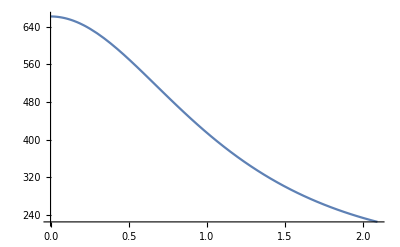

```mathematica
Plot[661.6/(1+661.6/511 *(1-Cos[x])),{x,0,120π/180}]
```

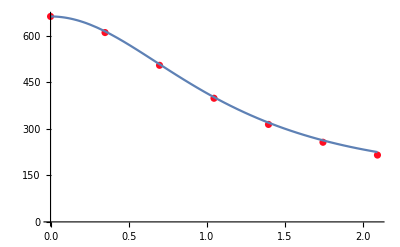

```mathematica
Show[%,%4]
```

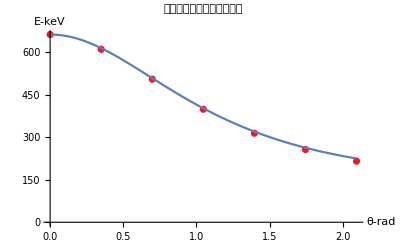

```mathematica
Show[%7,AxesLabel->{HoldForm[θ-rad],HoldForm[Ε-keV]},PlotLabel->HoldForm[散射光子能量与散射角关系],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
N[512437/48]
```

10675.8

```mathematica
f[x_]:=(1+662/511*(1-Cos[x]))^(-2)*(1+Cos[x]^2)/2*(1+(1-Cos[x])^2/((662/511)^(-2)(1+Cos[x]^2)(1+(662/511)*(1-Cos[x]))))
```

```mathematica
N[f[20/180*Pi]]
```

0.812435

```mathematica
N[Table[f[x*Pi*20/180]/f[20/180*Pi],{x,1,6}]]
```

{1.,0.600675,0.34106,0.22734,0.188656,0.179955}

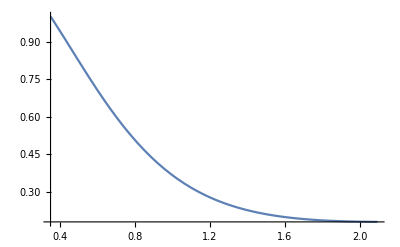

```mathematica
Plot[f[x]/f[20/180*Pi],{x,20/180*Pi,120/180*Pi}]
```

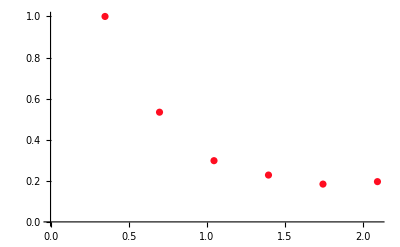

```mathematica
ListPlot[{{20π/180,1},{40π/180,0.534},{60π/180,0.298},{80π/180,0.228},{100π/180,0.184},{120π/180,0.196}},PlotStyle->RGBColor[1.,0.05,0.13]]
```

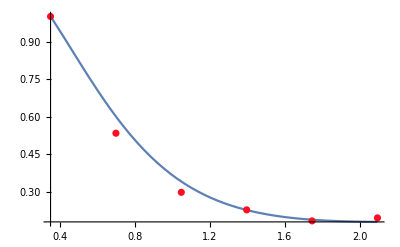

```mathematica
Show[%36,%38]
```

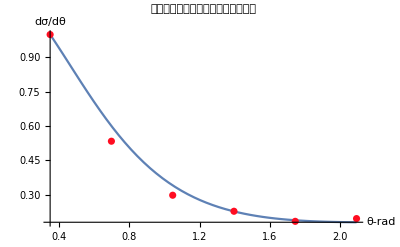

```mathematica
Show[%39,AxesLabel->{HoldForm[θ-rad],HoldForm[dσ/dθ]},PlotLabel->HoldForm[相对微分散射截面与散射角之间关系],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```